# Pure shear

## explore the numerical shear to a snapshot

### numerical function

```mathematica
numdericalϵ[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
strainback={{1-ddx,0},{0,1/(1-ddx)}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

```mathematica
numdericalEnergyStressϵ[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
strainback={{1-ddx,0},{0,1/(1-ddx)}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

```mathematica
numdericalCellg[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

### analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
ri={rix,riy}
rj={rjx,rjy}
rk={rkx,rky}
```

{rix,riy}

{rjx,rjy}

{rkx,rky}

```mathematica
hijk=voro[ri,rj,rk];
den=(rjx*rky-rjy*rkx)^3;
```

```mathematica
(*Analytical dirivatives of dhdr and dhdr*)
```

```mathematica
v1dri[r1_,r2_,r3_]:=(({{D[hijk[[1]],rix], D[hijk[[1]],riy]}, {D[hijk[[2]],rix], D[hijk[[2]],riy]}}))/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
```

```mathematica
v2drirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
v2driri[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rix],D[D[hijk[[2]],rix],rix]},
{D[D[hijk[[1]],riy],rix],D[D[hijk[[2]],riy],rix]}},
{{D[D[hijk[[1]],rix],riy],D[D[hijk[[2]],rix],riy]},
{D[D[hijk[[1]],riy],riy],D[D[hijk[[2]],riy],riy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
D[D[1/(1+ϵ),ϵ],ϵ]/.{ϵ->0}
D[1/(1+ϵ),ϵ]/.{ϵ->0}
```

2

-1

```mathematica
test={{{111,112},{211,212}},{{121,122},{221,222}}};
(test[[;;,;;,1]].{x1,y1}).{x2,y2}
```

x2 (111 x1+211 y1)+(121 x1+221 y1) y2

```mathematica
test={{{111,112},{121,122}},{{211,212},{221,222}}};
(test[[;;,;;,1]].{x2,y2}).{x1,y1}
```

x1 (111 x2+121 y2)+y1 (211 x2+221 y2)

```mathematica
(*Analytical dirivatives of dhdg and d2hdgdg*)
```

```mathematica
dridg={riy,0};
drjdg={rjy,0};
drkdg={rky,0};
(*dh2dgdg[r1_,r2_,r3_]:=(v2drirj[r1,r2,r3].{r2[[2]],0}).{r1[[2]],0}+(v2drirj[r1,r3,r2].{r3[[2]],0}).{r1[[2]],0}+(v2driri[r1,r2,r3].{r1[[2]],0}).{r1[[2]],0}+(v2drirj[r2,r1,r3].{r1[[2]],0}).{r2[[2]],0}+(v2drirj[r2,r3,r1].{r3[[2]],0}).{r2[[2]],0}+(v2driri[r2,r1,r3].{r2[[2]],0}).{r2[[2]],0}+(v2drirj[r3,r1,r2].{r1[[2]],0}).{r3[[2]],0}+(v2drirj[r3,r2,r1].{r2[[2]],0}).{r3[[2]],0}+(v2driri[r3,r1,r2].{r3[[2]],0}).{r3[[2]],0};*)
dh2dgdg[r1_,r2_,r3_]:={(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]};
dh2dϵdϵ[r1_,r2_,r3_]:={(v2driri[r1,r2,r3][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r1[[1]],-r1[[2]]}+(v2drirj[r1,r2,r3][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r1,r3,r2][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r3[[1]],-r3[[2]]}+
(v2driri[r2,r3,r1][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r2,r3,r1][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r2,r1,r3][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r1[[1]],-r1[[2]]}+(v2driri[r3,r2,r1][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r3,r2,r1][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r3,r1,r2][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r1[[1]],-r1[[2]]},(v2driri[r1,r2,r3][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r1[[1]],-r1[[2]]}+(v2drirj[r1,r2,r3][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r1,r3,r2][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r3[[1]],-r3[[2]]}+
(v2driri[r2,r3,r1][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r2,r3,r1][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r2,r1,r3][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r1[[1]],-r1[[2]]}+(v2driri[r3,r2,r1][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r3,r2,r1][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r3,r1,r2][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r1[[1]],-r1[[2]]}}+(v1dri[r1,r2,r3].{0,2r1[[2]]})+(v1dri[r2,r1,r3].{0,2r2[[2]]})+(v1dri[r3,r1,r2].{0,2r3[[2]]});
```

```mathematica
dhdg[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0});
```

```mathematica
dhdϵ[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[1]],-r1[[2]]})+(v1dri[r2,r1,r3].{r2[[1]],-r2[[2]]})+(v1dri[r3,r1,r2].{r3[[1]],-r3[[2]]});
```

```mathematica
(*For C++*)
r1={r1x,r1y};r2={r2x,r2y};r3={r3x,r3y};
```

```mathematica
CForm[Simplify[dhdϵ[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((-(r3y*(r2x*r2x)) + 3*r3y*(r2y*r2y) + r2y*(r3x*r3x) - 3*r2y*(r3y*r3y))/(2*r2y*r3x - 2*r2x*r3y),
   (3*r3x*(r2x*r2x) - r3x*(r2y*r2y) - 3*r2x*(r3x*r3x) + r2x*(r3y*r3y))/(2*r2y*r3x - 2*r2x*r3y))

```mathematica
CForm[Simplify[dh2dϵdϵ[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((6*r2y*(r2y - r3y)*r3y)/(-(r2y*r3x) + r2x*r3y),
   (3*r3x*(r2x*r2x) + r3x*(r2y*r2y) - 3*r2x*(r3x*r3x) - r2x*(r3y*r3y))/(r2y*r3x - r2x*r3y))

```mathematica
(*Numerical test*)
p1={15.764422379230995,17.23195769060852};p2={16.240740458209697,16.83431037696828};p3={15.803192711415326,16.385277852647548};
```

```mathematica
(*This verifies dhdϵ and d2hdϵdϵ*)
strainfor={{1+0.0001,0},{0,1/(1+0.0001)}};
strainback={{1-0.0001,0},{0,1/(1-0.0001)}};
hForward=voro[strainfor.p1,strainfor.p2,strainfor.p3];
hback=voro[strainback.p1,strainback.p2,strainback.p3];
originalh=voro[p1,p2,p3];
(hback+hForward-2*originalh)/0.0001^2
-(hback-hForward)/0.0002
```

{-2.33861,33.6619}

{16.5959,-16.7684}

```mathematica
dh2dϵdϵ[p1,p2,p3]
dhdϵ[p1,p2,p3]
```

{-2.33861,33.6619}

{16.5959,-16.7684}

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
energy[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
KP*(peri[hv]-PP)^2+KA*(area[hv]-PA)^2
]
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
Simplify[dhdϵ[r1,r2,r3]]
```

{(r2y r3x^2+3 r1y^2 (r2y-r3y)-r2x^2 r3y+3 r2y^2 r3y-3 r2y r3y^2+r1x^2 (-r2y+r3y)+r1y (r2x^2-3 r2y^2-r3x^2+3 r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))),(3 r1x^2 (r2x-r3x)+3 r2x^2 r3x-r2y^2 r3x-3 r2x r3x^2+r1y^2 (-r2x+r3x)+r2x r3y^2+r1x (-3 r2x^2+r2y^2+3 r3x^2-r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y)))}

```mathematica
Simplify[dh2dϵdϵ[r1,r2,r3]]
```

{(6 (r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(3 r1x^2 (r2x-r3x)+r1y^2 (r2x-r3x)+3 r2x^2 r3x+r2y^2 r3x-3 r2x r3x^2-r2x r3y^2+r1x (-3 r2x^2-r2y^2+3 r3x^2+r3y^2))/(r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))}

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdϵGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r2y r3x^2+3 r1y^2 (r2y-r3y)-r2x^2 r3y+3 r2y^2 r3y-3 r2y r3y^2+r1x^2 (-r2y+r3y)+r1y (r2x^2-3 r2y^2-r3x^2+3 r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))),(3 r1x^2 (r2x-r3x)+3 r2x^2 r3x-r2y^2 r3x-3 r2x r3x^2+r1y^2 (-r2x+r3x)+r2x r3y^2+r1x (-3 r2x^2+r2y^2+3 r3x^2-r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y)))}
];

d2hdϵdϵGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(6 (r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(3 r1x^2 (r2x-r3x)+r1y^2 (r2x-r3x)+3 r2x^2 r3x+r2y^2 r3x-3 r2x r3x^2-r2x r3y^2+r1x (-3 r2x^2-r2y^2+3 r3x^2+r3y^2))/(r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))}
];
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidϵdϵGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdϵGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdϵGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdϵdϵGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
];
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidϵGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdϵGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
Analyticalϵ[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Sum[{energy[voronoiPolygons[[cellIndex[[i]]]][[1]],KA,KP,PA,PP],deidϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidϵdϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalgCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
(*function to varry ep*)
```

```mathematica
numdericalPureShear[allPoints_,box_List,pointID_List,ddx_,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,strainfor,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
allPointsPBD=strainfor.#&/@allPointsPBD;
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Sum[{energy[voronoiPolygons[[cellIndex[[i]]]][[1]],KA,KP,PA,PP],deidϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidϵdϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

### load a random configuration

```mathematica
data=Import["/Users/chengling/Downloads/nvt_stress_tensor_N100_p3.800_T0.10000000_0.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/energy→NumericArray[…],/neighbor→NumericArray[…],/position→NumericArray[…],/sigma→NumericArray[…],/time→NumericArray[…]|>

```mathematica
positions=Table[{data[[5,2]][[2*i+1]],data[[5,2]][[2*i+2]]},{i,0,99}];
```

```mathematica
ana=Analyticalϵ[positions,{10,10},Table[i,{i,100}],1,1,1,3.80];
```

```mathematica
ana
```

{23.9024,12.7964,710.566}

```mathematica
intial=numdericalPureShear[positions,{10,10},Table[i,{i,100}],0,1,1,1,3.80]
```

{20.3049,18.5768,435.75}

```mathematica
epsilons=Table[10^(-4+ep*0.1),{ep,0,30}]
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1}

```mathematica
epsilons[[1]]
```

0.0001

```mathematica
Table[ep,{ep,epsilons}]
```

{0,0.00001,0.00005,0.0001,0.001,0.01,0.02,0.04,0.08,0.1}

```mathematica
numePureShear=Table[numdericalPureShear[positions,{10,10},Table[i,{i,100}],ep,1,1,1,3.80],{ep,epsilons}];
```

```mathematica
numePureShear
```

{{20.3068,18.6223,435.821},{20.3073,18.634,435.84},{20.3079,18.6488,435.863},{20.3087,18.6675,435.893},{20.3096,18.691,435.93},{20.3108,18.7205,435.977},{20.3124,18.7578,436.037},{20.3143,18.8046,436.113},{20.3167,18.8636,436.21},{20.3198,18.9379,436.334},{20.3237,19.0315,436.492},{20.3287,19.1494,436.696},{20.3349,19.2978,436.959},{20.3429,19.4848,437.301},{20.353,19.7205,437.748},{20.3659,20.0174,438.338},{20.3823,20.3919,439.122},{20.4035,20.8642,440.177},{20.4308,21.4604,441.61},{20.4658,20.6955,438.154},{20.51,19.0658,444.57},{20.5603,20.2558,445.756},{20.6278,21.7592,447.909},{20.7194,23.6637,451.655},{20.845,26.0865,457.99},{21.0198,29.1895,468.492},{21.2663,33.2046,485.646},{21.5792,34.2066,489.26},{21.9546,29.2388,503.326},{22.4724,39.2122,537.08},{23.2201,33.6655,557.142}}

```mathematica
(numePureShear[[2,1]]-numePureShear[[1,1]])/epsilons[[2]]
```

1.29738

```mathematica
Table[epsilons[[i]],numePureShear[[i,1]]-numePureShear[[1,1]],{i,2,10}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Table::nliter: Non-list iterator numePureShear⟦i,1⟧-numePureShear⟦1,1⟧ at position 2 does not evaluate to a real numeric value.

Table[epsilons⟦i⟧,numePureShear⟦i,1⟧-numePureShear⟦1,1⟧,{i,2,10}]

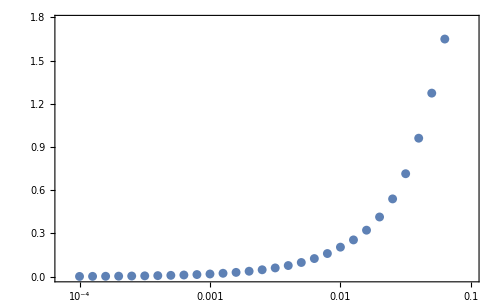

```mathematica
ListLogLinearPlot[Table[{epsilons[[i]],numePureShear[[i,1]]-intial[[1]]},{i,Length[epsilons]}]]
```

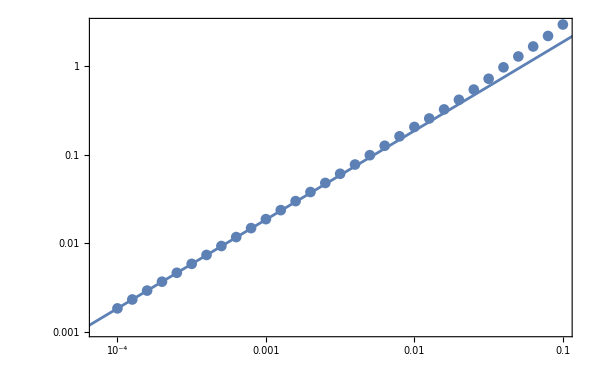

```mathematica
Show[ListLogLogPlot[Table[{epsilons[[i]],numePureShear[[i,1]]-intial[[1]]},{i,Length[epsilons]}]],LogLogPlot[x*intial[[2]],{x,0.000001,1}]]
```

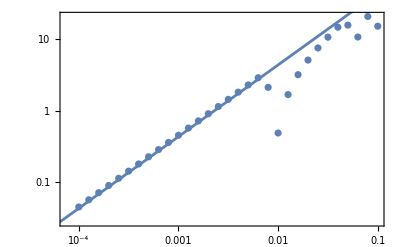

```mathematica
Show[ListLogLogPlot[Table[{epsilons[[i]],numePureShear[[i,2]]-intial[[2]]},{i,Length[epsilons]}]],LogLogPlot[x*intial[[3]],{x,0.000001,1}]]
```

## preliminary data

### load data

```mathematica
p0s={3.825}
```

{3.825}

```mathematica
temperatures={{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015}};
 records={{10}};
epsilons={{-0.01,0.,0.01},{-0.05,0.,0.05}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
pureShearDerivatives=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/pureShearDerivatives1st2nd_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/timeEnergy_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

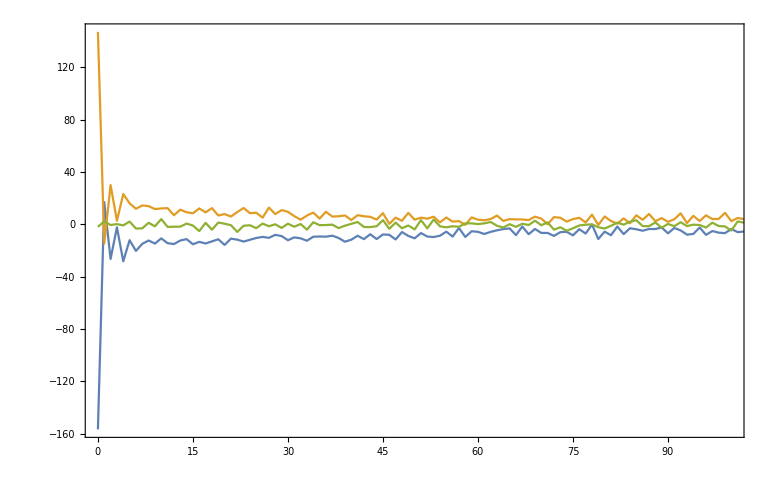

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,2,1,1,1,i]],pureShearDerivatives[[1,12,2,1,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,2,3,1,1,i]],pureShearDerivatives[[1,12,2,3,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,2,3,1,1,i]],pureShearDerivatives[[1,12,2,2,1,1,i]]},{i,10000}]},PlotRange->{{0,100},All},Joined->True]
```

```mathematica
energyplots=Table[ListPlot[{Table[{timeEnergy[[1,T,2,1,1,1,i]],timeEnergy[[1,T,2,1,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,T,2,3,1,1,i]],timeEnergy[[1,T,2,3,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,T,2,3,1,1,i]],timeEnergy[[1,T,2,2,1,2,i]]},{i,10000}]},FrameLabel->{"t","E"},PlotLabel->"T="<>ToString[temperatures[[1,T]]],PlotRange->{{0,50},All},Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

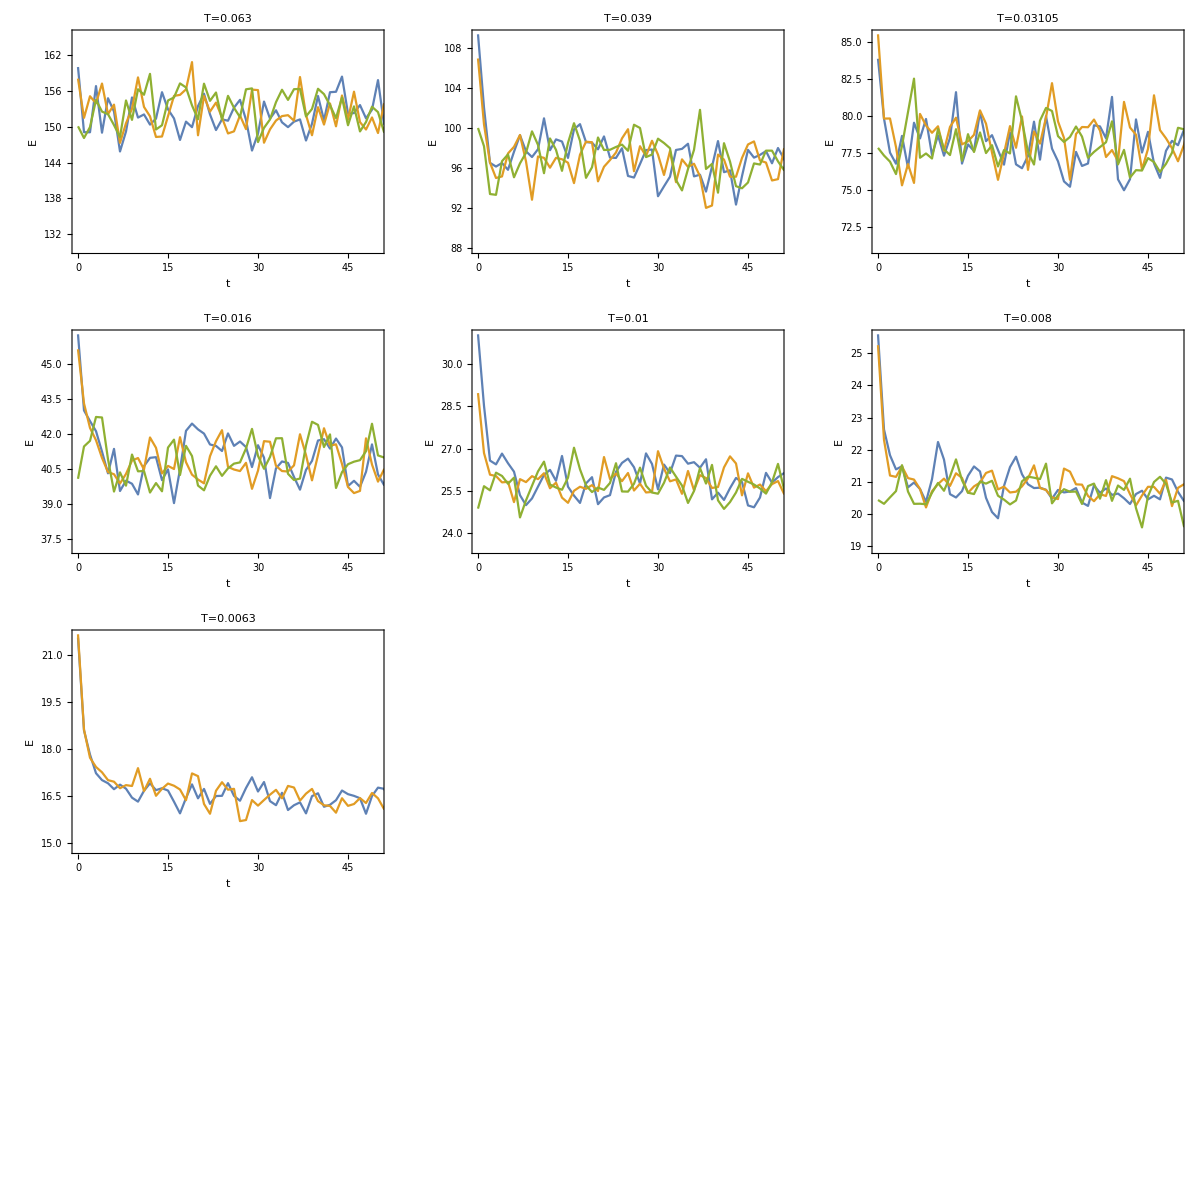

```mathematica
energyTra=Grid[Partition[energyplots,3]]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/energytra.jpeg",energyTra,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/energytra.jpeg

```mathematica
Normal[pureShearDerivatives[[1,1,1,1,1,1]]]
```

```mathematica
wind=
```

```mathematica
stressplots=Table[ListPlot[{Table[{timeEnergy[[1,T,2,1,1,1,i]],Mean[Table[pureShearDerivatives[[1,T,2,1,1,1,i]]]]},{i,10000}],Table[{timeEnergy[[1,T,2,3,1,1,i]],pureShearDerivatives[[1,T,2,3,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,T,2,3,1,1,i]],pureShearDerivatives[[1,T,2,2,1,1,i]]},{i,10000}]},FrameLabel->{"t","de/dγ"},PlotLabel->"T="<>ToString[temperatures[[1,T]]],PlotRange->{{0,100},All},Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

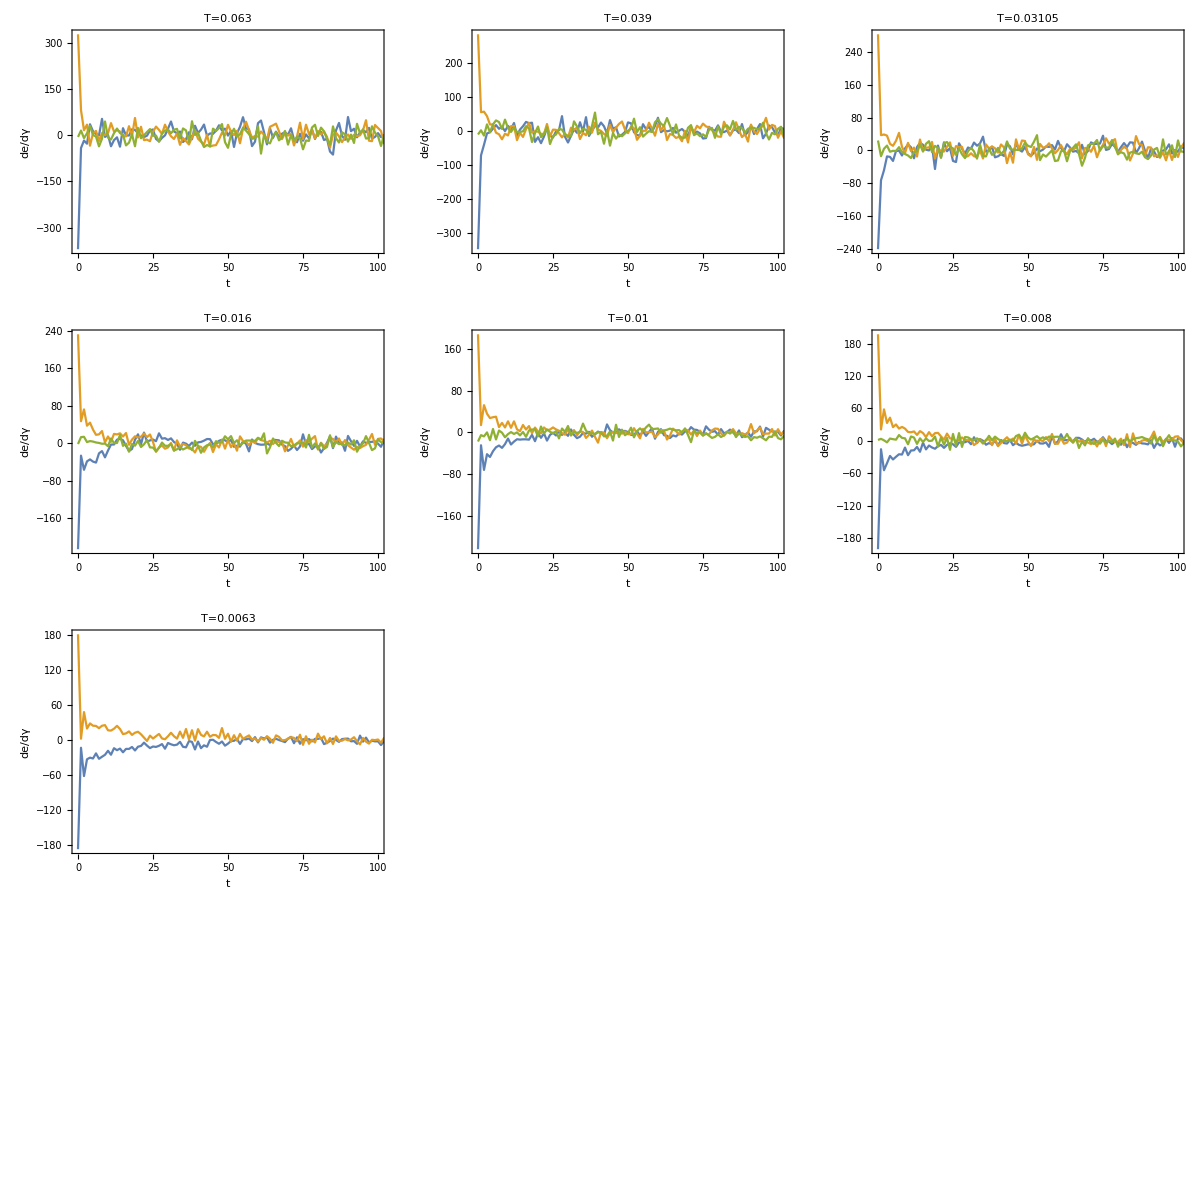

```mathematica
stressTra=Grid[Partition[stressplots,3]]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/stresstra.jpeg",stressTra,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/stresstra.jpeg

```mathematica
σ
```

```mathematica
numericalGplots=Table[ListLogLinearPlot[Table[{timeEnergy[[1,T,2,1,1,1,i]],(pureShearDerivatives[[1,T,2,3,1,1,i]]-pureShearDerivatives[[1,T,2,1,1,1,i]])/0.1/4096},{i,10000}],FrameLabel->{"t","G"},PlotLabel->"T="<>ToString[temperatures[[1,T]]],PlotRange->{{0,1000},All},Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

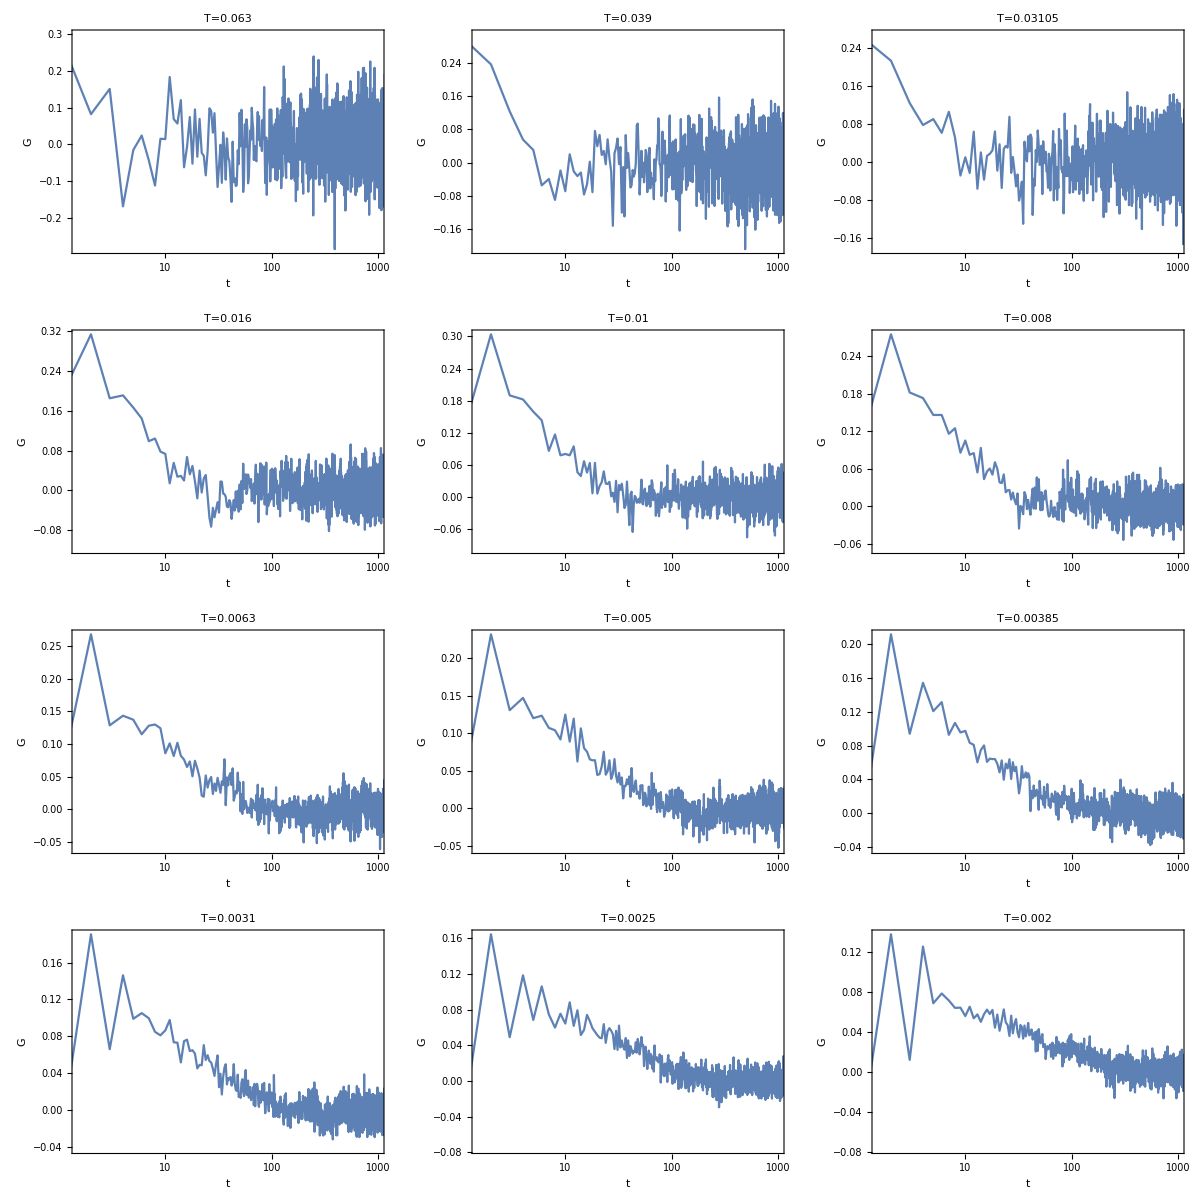

```mathematica
GTra=Grid[Partition[numericalGplots,3]]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/Gtra.jpeg",GTra,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/Gtra.jpeg

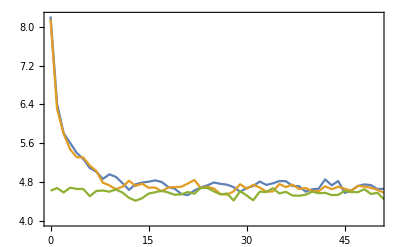

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,2,1,1,1,i]],timeEnergy[[1,Length[temperatures[[1]]],2,1,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,2,3,1,1,i]],timeEnergy[[1,Length[temperatures[[1]]],2,3,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,2,3,1,1,i]],timeEnergy[[1,Length[temperatures[[1]]],2,2,1,2,i]]},{i,10000}]},PlotRange->{{0,50},All},Joined->True]
```

```mathematica
Dimensions[timeEnergy]
```

{1,1,2,3,1}

```mathematica
g1=Table[Table[
Table[Table[Mean[Normal[pureShearDerivatives[[p,T,ep,2,rec,2]]]],{rec,Length[records[[p]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
g1*0.05^2
```

{{{{27.0948},{27.0948}},{{21.7683},{21.7683}},{{19.5711},{19.5711}},{{14.4179},{14.4179}},{{11.7389},{11.7389}},{{10.719},{10.719}},{{9.7994},{9.7994}},{{9.05463},{9.05463}},{{8.34697},{8.34697}},{{7.88169},{7.88169}},{{7.50981},{7.50981}},{{7.18712},{7.18712}},{{6.87369},{6.87369}}}}

```mathematica
SACtimeMean={{{7.1178234044669215*^-6,7.044274046517541*^-6,6.968002715064671*^-6,6.8892169141219806*^-6,6.807885203068163*^-6,6.724070601657067*^-6,6.637874133697232*^-6,6.549358900408858*^-6,6.4587117347488585*^-6,6.366079345083086*^-6,6.271444953264346*^-6,6.175008773062679*^-6,6.076763639601284*^-6,5.976856517553409*^-6,5.8754628866803125*^-6,5.772742079805105*^-6,5.668631951490706*^-6,5.457734704620998*^-6,5.2437260300166316*^-6,5.027724099962484*^-6,4.811044322995669*^-6,4.594852099199163*^-6,4.38033802088355*^-6,4.168617069896147*^-6,3.9618489785940245*^-6,3.5616844645687078*^-6,3.187510596459346*^-6,2.8448041440235264*^-6,2.537327767333261*^-6,2.2672733819268275*^-6,2.034940430247089*^-6,1.839180133112889*^-6,1.6856478624804652*^-6,1.4522177174508465*^-6,1.315175720754887*^-6,1.2432311200220348*^-6,1.206921943403648*^-6,1.1833199392243506*^-6,1.1597845623270955*^-6,1.1295158847894578*^-6,1.089137274078573*^-6,9.978195091790168*^-7,9.047790400908198*^-7,8.191034367461744*^-7,7.362276909001269*^-7,6.491922347703798*^-7,5.633812548300924*^-7,4.850233759016007*^-7,4.2278107029722047*^-7,3.2198576063469096*^-7,2.414043714195336*^-7,1.8137511445536368*^-7,1.421485983292552*^-7,1.1026892630436975*^-7,8.536319926919271*^-8,6.480607441287183*^-8,6.330248455583313*^-8,4.7440794443716696*^-8,1.8014206808918557*^-8,1.367939971331862*^-8,2.0987298174092757*^-8,5.696660288234063*^-9,3.5562523238649208*^-9,6.838423572288708*^-10,-1.2918147061349297*^-8,-1.8318252937530205*^-8,-6.0414278820638375*^-9,-8.185613244676624*^-9,-1.0519347127277193*^-8,-1.8226084403269753*^-8,-5.559746612381627*^-9,5.669295742823799*^-9,4.341728711501803*^-9,-8.547898173664168*^-9,-1.4962140370922686*^-8,-1.6905382967522618*^-9,-1.1017492548378462*^-8,-1.1607340811688701*^-8,4.242454520684634*^-9,1.15714372735558*^-8,4.556653939981412*^-9,-1.6958491238201317*^-9,1.0016518679131295*^-8,8.419098533028418*^-9,-1.8452840726766737*^-9,-7.533465005644857*^-10,-6.653888607330709*^-11,-8.23534519752633*^-9,-5.446575411828476*^-9,7.566589221614931*^-9,-5.121106757564926*^-9,-1.7970998315085882*^-8,9.70136213458451*^-9,-9.89444687418284*^-9,1.1715447692820408*^-8,1.8144417582801771*^-9,1.3114855365296113*^-9,3.9218668091656054*^-10,9.710626983584629*^-9,-5.035534306637721*^-9,-6.370631393108011*^-9,-3.2187415652936717*^-9,-9.370208413047174*^-9,-2.7699415159840336*^-10,-2.3690442517437906*^-9,4.785550076985188*^-10,6.262458688581913*^-9,2.0360036306214622*^-10,-4.9995899974480685*^-9,-5.671323876280863*^-9,-4.2440308705153875*^-9,-2.2242786265026684*^-10,-4.926467599763929*^-10,-5.388041251479269*^-9,7.426350207371231*^-10,4.042876620967902*^-9,-1.8886764982008584*^-9,-1.4958746816488672*^-9,4.840546554615051*^-9,-2.8472706336579815*^-11,-1.6417278056749735*^-9,3.76690535099199*^-10,1.834306157188437*^-9,2.4134374684872273*^-9,2.8211728292424275*^-9,-4.7631219893156325*^-9,2.1621504746180185*^-9,-5.743662630072176*^-10,1.8085264229614877*^-9,-3.3151252522196304*^-9,2.837932536534166*^-10,-2.4838922842227885*^-9,1.8570803017333663*^-9,-1.1894491659944928*^-10,2.4086651270522655*^-9,-1.6694729200489404*^-9,-2.097891389279706*^-10,5.815353057364717*^-10,1.1813948654318779*^-9,5.412199138727689*^-9},{3.87684184248266*^-6,3.84875280770454*^-6,3.818979049199913*^-6,3.787538277669304*^-6,3.754447861633674*^-6,3.7197736587863103*^-6,3.683540871220321*^-6,3.645797808424861*^-6,3.6066096617136317*^-6,3.5660256593067947*^-6,3.5240870961274654*^-6,3.4808685694563884*^-6,3.4364095915205958*^-6,3.390804632434392*^-6,3.3440814248976523*^-6,3.2963298933779952*^-6,3.2473530179884465*^-6,3.1472547792231075*^-6,3.0441220258291385*^-6,2.938519523186726*^-6,2.831121868318806*^-6,2.7224614762348473*^-6,2.6131296811494374*^-6,2.5037628483284366*^-6,2.3951700133002134*^-6,2.181547792685639*^-6,1.9761269830229594*^-6,1.782316065322962*^-6,1.6029805556748092*^-6,1.4400176552653127*^-6,1.2944932199455333*^-6,1.1672196616706058*^-6,1.062583908955702*^-6,8.956952868641095*^-7,7.894462261788973*^-7,7.313072171917913*^-7,7.072261199507195*^-7,7.046998845253819*^-7,7.137023521447957*^-7,7.276597964158023*^-7,7.414118474810197*^-7,7.595031074602716*^-7,7.56693767399072*^-7,7.282595396030868*^-7,6.780430636038723*^-7,6.14523476605659*^-7,5.499733813469671*^-7,4.946341688766119*^-7,4.521288456074623*^-7,3.8374453563094013*^-7,3.2850888851932486*^-7,2.780777258200469*^-7,2.2789393597102845*^-7,1.891729248211074*^-7,1.6793151813990104*^-7,1.5248246515611965*^-7,1.2865200856008085*^-7,9.060140973392094*^-8,7.648379986932814*^-8,5.612913295881708*^-8,3.519918978512499*^-8,2.5420821977835318*^-8,2.5654758077647966*^-8,3.1133527101396307*^-8,2.2234546975296527*^-8,5.008746655244281*^-9,5.0313333178274165*^-9,1.7505709427513954*^-9,-4.278796376299925*^-10,6.9596487201817276*^-9,2.9171653914563967*^-9,-2.26904494107665*^-9,4.968165406961572*^-9,6.061377832618657*^-9,-3.913880593363779*^-9,-9.860573428467877*^-9,-8.891779285093211*^-9,-3.6071353930940847*^-9,-4.121299252798799*^-9,5.970973942641862*^-9,1.4290669052974543*^-8,3.685556573091348*^-10,5.425904326000212*^-9,5.570865761941931*^-9,2.0209992379086438*^-10,-3.924709581084549*^-9,-3.737919039775146*^-9,-5.506214830671485*^-9,-5.8408388540979635*^-9,-8.614900785617051*^-9,-1.2741110915400303*^-8,-1.7009438145059697*^-8,-1.0264459776554288*^-8,-2.377189782853856*^-9,-1.1270278172460704*^-8,-9.68085419785303*^-9,-4.114615727260835*^-9,-5.3262512104321875*^-9,-3.031538601993632*^-9,5.728845815066449*^-9,3.984145385002866*^-9,-1.1784229110812542*^-9,-6.505838107533485*^-10,1.12281111465435*^-9,-2.170323791946282*^-9,5.499398952216279*^-9,-5.249495025225544*^-9,-2.2960493039182387*^-9,-3.1050789600688*^-9,-4.5021065748466225*^-9,2.15790408480669*^-9,-6.035371791778437*^-9,-1.0816776992484862*^-9,-1.2818232922350385*^-9,6.076784536358137*^-10,-2.59259852236818*^-9,-5.684512109276371*^-9,3.0322922223030843*^-9,-9.137443471037258*^-11,7.276438204966061*^-10,1.7491266165322012*^-9,-6.454360119827166*^-10,-1.545527837486762*^-9,-6.94943140132042*^-10,4.1071262922851*^-9,3.042378797899996*^-9,-2.377007001286572*^-9,-2.204937121747633*^-9,-1.260753849393459*^-9,-4.083844541223871*^-9,2.2556919842981076*^-9,2.1847893404954284*^-10,7.297303941626258*^-10,1.243794984322487*^-9,2.0555043849935263*^-9,-3.188803841448517*^-9,-1.0023975273836092*^-9,-5.369552521744023*^-10,2.2925096530606624*^-9,6.805473629648692*^-10},{2.8602665618366654*^-6,2.8426600802432924*^-6,2.8237365995126583*^-6,2.8035200253288326*^-6,2.782056931333407*^-6,2.759351411900686*^-6,2.7354445236277255*^-6,2.7103472620063128*^-6,2.6841026420351513*^-6,2.656750255164737*^-6,2.628318819449969*^-6,2.5988558389058872*^-6,2.5683950936965293*^-6,2.5369973876672324*^-6,2.5047090395679163*^-6,2.4715795456053046*^-6,2.4374573901500893*^-6,2.3673529347177115*^-6,2.294636243383927*^-6,2.219732072281943*^-6,2.143006868336122*^-6,2.0649233932296975*^-6,1.9859064448935334*^-6,1.9064033320596136*^-6,1.8269732623567678*^-6,1.66953741582835*^-6,1.516409322536008*^-6,1.3702660991883371*^-6,1.2332260790776428*^-6,1.1070333710151693*^-6,9.929795689996705*^-7,8.919000185501361*^-7,8.073859498714805*^-7,6.700599257752033*^-7,5.79628979230982*^-7,5.283914984440797*^-7,5.074360642675644*^-7,5.076690107475022*^-7,5.2109676368397*^-7,5.409844003249959*^-7,5.625061758424053*^-7,5.994325344230892*^-7,6.173763127062036*^-7,6.098217038163796*^-7,5.786852138042617*^-7,5.313733429114159*^-7,4.793413647887125*^-7,4.318458696622275*^-7,3.948601311675319*^-7,3.3436328180229137*^-7,2.8933120981666984*^-7,2.570324504443246*^-7,2.292345969362084*^-7,2.0081043936026372*^-7,1.78484320334219*^-7,1.6081621235652726*^-7,1.398018302585847*^-7,1.0477452383172889*^-7,8.296204063075331*^-8,6.608699242734431*^-8,4.397011738886404*^-8,3.298014900752993*^-8,2.562658736755872*^-8,1.7952918036443833*^-8,1.1554131770043106*^-8,-3.939545070893015*^-9,-5.7187395231258915*^-9,-6.529389393009257*^-9,-2.9841548598269005*^-9,-1.3534304046426179*^-8,-7.466463347223203*^-9,-1.2609095499216795*^-8,-8.75653141981419*^-9,-8.98531479475591*^-9,5.72397162344893*^-11,-1.8916908078970883*^-9,-6.95633294290093*^-9,-8.287299975267342*^-9,-1.4532447610978934*^-9,2.577520620865119*^-9,2.402546854171133*^-9,3.078997651616168*^-9,4.208882549719429*^-9,1.4854347335861405*^-9,-2.3436807233369763*^-9,-7.553361815425388*^-9,6.743371366706728*^-10,1.8694874611698376*^-10,-5.716055443212612*^-9,-3.3623659145504186*^-9,1.1623154119356825*^-9,1.114567329374393*^-9,1.8465433151550522*^-9,5.855076409148404*^-9,-9.81744832688276*^-9,-6.0416985298432855*^-9,-4.025119063190303*^-9,4.1292969469903594*^-10,2.4458887192824086*^-9,-1.2310058085221074*^-9,4.431800559071223*^-9,2.7771656838612096*^-9,1.8401963473476919*^-9,-4.451035959698742*^-9,-2.8793170280188054*^-9,2.1966827906174326*^-9,3.27870400543856*^-9,2.794142148077556*^-9,-1.7191955124396134*^-9,-3.7021995637139156*^-9,3.9486640134514605*^-9,-1.520837088081752*^-10,2.3386238889634787*^-9,-1.6735153307335294*^-9,-9.098521457725332*^-10,1.4931974950492142*^-9,5.837916834340152*^-10,-5.64713955028791*^-10,2.9992380378956914*^-9,-2.3772271713878855*^-9,2.2201115120721156*^-9,1.0973750779856845*^-9,-2.6120412260448242*^-9,-2.0965340469078045*^-9,1.9917349408474332*^-10,-5.006698809018237*^-10,-2.8244542001975446*^-9,9.084528700017475*^-10,1.6171634491958986*^-9,-1.0915996330394144*^-9,-6.721754999243822*^-10,3.46077900866633*^-10,3.595792650702553*^-10,-1.5212108932568603*^-9,-2.61400825594977*^-9,2.180708812323362*^-9,6.563888544082864*^-10,1.92396108334151*^-9,1.0695758656546975*^-10,7.53010229408683*^-11},{1.1767017392495776*^-6,1.172292143191193*^-6,1.1672971530436565*^-6,1.1617287231304009*^-6,1.1555925175881721*^-6,1.1489011101658708*^-6,1.141659514067535*^-6,1.1338720260768892*^-6,1.1255555891898118*^-6,1.116722682716467*^-6,1.1073852778815727*^-6,1.0975600926336513*^-6,1.0872581423562461*^-6,1.0764931867844224*^-6,1.06527879092209*^-6,1.0536351590577972*^-6,1.0414806061958017*^-6,1.0162005289034592*^-6,9.89466994938878*^-7,9.614372071512892*^-7,9.322732871940225*^-7,9.021356728350122*^-7,8.711816219908858*^-7,8.395804062084684*^-7,8.07410542069205*^-7,7.425062595496056*^-7,6.775359847296871*^-7,6.136704119003511*^-7,5.519746871311698*^-7,4.933611384734342*^-7,4.386168980343672*^-7,3.883714372771114*^-7,3.443922575268563*^-7,2.696691514285871*^-7,2.1616591633667452*^-7,1.826362935473409*^-7,1.6672294380739435*^-7,1.6539422517832879*^-7,1.7533001065575486*^-7,1.9324465440552745*^-7,2.167333513704402*^-7,2.6610676265365247*^-7,3.082006893658382*^-7,3.3176097969289387*^-7,3.3326050528358323*^-7,3.1643706806926093*^-7,2.9011077092885663*^-7,2.632222406261314*^-7,2.426911486645131*^-7,2.1541947232737646*^-7,2.0339893067014729*^-7,1.9611925373338905*^-7,1.862084865982219*^-7,1.7370074612079477*^-7,1.6171897242653106*^-7,1.505945512938214*^-7,1.414530549742009*^-7,1.2594087107261697*^-7,1.1263378062582488*^-7,9.905121727461668*^-8,8.900675485481435*^-8,7.852162700347725*^-8,6.944267127973127*^-8,6.02234334460385*^-8,5.548272108757144*^-8,4.2641344955380215*^-8,3.156493165439654*^-8,2.4150096955959497*^-8,2.0096681499142714*^-8,1.510267115727474*^-8,1.1369718303645815*^-8,8.463942261196291*^-9,8.296421092059316*^-9,6.537691965789538*^-9,6.291493531269524*^-9,4.469672438873607*^-9,-1.2660263133049804*^-9,2.3304979444547507*^-9,2.860098095682577*^-9,6.180499665854438*^-10,2.1231221889875545*^-9,3.600550486498658*^-10,-3.3157982244711813*^-9,-3.304165366145487*^-9,-3.1055723451321736*^-9,-1.5361017998466567*^-9,-1.1069219100663426*^-10,2.7316548668053538*^-9,4.426035704326539*^-9,1.6468207635257752*^-9,1.1841946609956511*^-9,-2.370838080813755*^-9,-2.4933872275122147*^-9,-7.061640655949569*^-10,1.6052496806260535*^-9,1.134945042112507*^-9,7.91396173309774*^-10,1.0792472801674969*^-9,-6.161459078628367*^-10,-9.778890630883758*^-10,3.0597756108621237*^-9,-4.5667626170672233*^-10,1.760947112639946*^-9,4.317482201187108*^-10,-3.03973741488986*^-10,-9.956084334155132*^-10,-1.8344201906413183*^-9,-2.165046083178369*^-9,1.4151345016339431*^-9,9.53601092936044*^-10,1.7964758390524175*^-9,-2.0304164829525891*^-10,-9.885370693747668*^-10,-1.4113420126732524*^-9,9.117710814500168*^-10,1.9777936349284106*^-9,-6.832504754186518*^-10,-1.652374582839502*^-9,1.301571625497776*^-9,-8.438006994411947*^-10,7.516414186442423*^-10,3.724462942530212*^-10,1.5744066655747777*^-9,9.438799912056046*^-10,-7.68072412235207*^-10,4.975963179203482*^-10,9.877982966920126*^-10,-4.4289536985329015*^-10,6.190100801905132*^-10,6.97051707756911*^-10,-8.274766328424461*^-10,-2.4372777569947996*^-10,9.214119933140577*^-10,9.915370855042528*^-10,9.216525189477079*^-10,-1.1201854561751678*^-9,-4.024020263529423*^-10,1.683138693824952*^-9,1.217948134417356*^-9,5.275384755118055*^-11},{6.237076432101302*^-7,6.220676216595952*^-7,6.201052178023835*^-7,6.178252660873757*^-7,6.152311964182036*^-7,6.123274303266294*^-7,6.091169715070723*^-7,6.056043063721248*^-7,6.017921568827051*^-7,5.976884905941076*^-7,5.932971528925484*^-7,5.886243568419641*^-7,5.836783528895647*^-7,5.784648863227551*^-7,5.729924706108524*^-7,5.672650447623022*^-7,5.612317860282507*^-7,5.485895728362606*^-7,5.350659600612073*^-7,5.207336657675595*^-7,5.056685278948384*^-7,4.899541684469102*^-7,4.736657778490971*^-7,4.5688925056077985*^-7,4.396250602075308*^-7,4.044039850011999*^-7,3.685372488681639*^-7,3.326601519101579*^-7,2.973653701426358*^-7,2.631997863465119*^-7,2.306563434632636*^-7,2.001473762408121*^-7,1.7266840412973575*^-7,1.2456373511983022*^-7,8.810730108455982*^-8,6.355259114522286*^-8,5.0292746128754974*^-8,4.70905375818559*^-8,5.233602943358108*^-8,6.418033144279592*^-8,8.137852124077285*^-8,1.1993081975836056*^-7,1.5600437601059632*^-7,1.7992230728356767*^-7,1.8770672354666871*^-7,1.811275402143232*^-7,1.658624508978712*^-7,1.4843679529741126*^-7,1.349019906869741*^-7,1.1962958636018663*^-7,1.1858471101333623*^-7,1.21034313375073*^-7,1.1833895813925564*^-7,1.1095138679898471*^-7,1.038450336446925*^-7,9.8970652458274*^-8,9.570790305104566*^-8,8.935674800727078*^-8,8.247811965601296*^-8,7.553993015763389*^-8,7.098212959535135*^-8,6.587751168889005*^-8,6.03243465364957*^-8,5.681418923241999*^-8,5.432567379677938*^-8,4.682436125334096*^-8,4.212641046251512*^-8,3.499530362153188*^-8,3.2409777116344246*^-8,2.759677683692702*^-8,2.4551503366102024*^-8,2.0273230897845603*^-8,1.8279393400572926*^-8,1.436523095651198*^-8,1.1510818477706172*^-8,1.0107484910702016*^-8,8.662257528368443*^-9,7.261921483930956*^-9,5.79591236836072*^-9,4.9530969770806765*^-9,4.556125753839159*^-9,3.58889944167979*^-9,9.244063497110624*^-10,-4.845734385748613*^-10,-2.029623702051937*^-9,6.124670448470131*^-10,5.749376471843422*^-10,1.6254776454939259*^-9,3.493506167482729*^-9,2.8862008797916593*^-9,3.6465291820135126*^-9,3.2950356093238257*^-9,1.0845835342459392*^-9,-1.6189065915174172*^-9,-1.2232233966109493*^-9,1.14348017413137*^-9,3.282328193644367*^-11,-2.9867761550803873*^-9,-2.5360873461097287*^-9,-1.562340468427949*^-9,-6.838474956564983*^-10,-3.9042079305819794*^-11,-7.864102893372898*^-10,3.591259286052025*^-10,5.876302918543927*^-11,-8.614311867055819*^-10,-2.565909222061711*^-10,-7.840753709027511*^-10,-5.92878539759678*^-10,4.959570364871607*^-10,8.123466443624859*^-12,-2.616163215928884*^-10,6.265953531937587*^-10,7.609607724245604*^-10,1.3401579028105806*^-9,-1.972418295714458*^-9,9.381035737253974*^-10,2.1740859074238805*^-9,-4.48393375319426*^-10,-6.682075867683181*^-10,-6.545326164546342*^-10,3.107552810942042*^-10,1.4057161391681257*^-9,9.395802683567976*^-10,-9.91381815522205*^-10,1.4101545211220925*^-10,1.422760577392285*^-9,4.4185940466525593*^-10,-2.8889052470675525*^-10,-4.3336980346554655*^-10,7.692772327570314*^-10,4.859089134553852*^-10,-2.73622475237519*^-10,-5.776331573454086*^-10,3.0895562513260666*^-10,9.705223061122952*^-10,8.547814713325451*^-10,-4.632230864118003*^-10,4.872123221135497*^-11,-2.751608640508113*^-10},{4.612415405816504*^-7,4.6021802281438115*^-7,4.5895314755680896*^-7,4.5744839498767986*^-7,4.5570545939001774*^-7,4.5372669966218973*^-7,4.5151492716537813*^-7,4.49073984578545*^-7,4.4640689376395775*^-7,4.4351837925822073*^-7,4.4041256321053554*^-7,4.370934340297442*^-7,4.335635220879448*^-7,4.2982949564126244*^-7,4.258952338005331*^-7,4.2176550603831776*^-7,4.173995255296123*^-7,4.0821851411867757*^-7,3.9835287769045824*^-7,3.8785192671601195*^-7,3.7677228360244025*^-7,3.651710647251006*^-7,3.531032818499669*^-7,3.406272479521356*^-7,3.277320726467543*^-7,3.013101783059037*^-7,2.7421939773621024*^-7,2.4693007163151007*^-7,2.198937672666018*^-7,1.935333223469655*^-7,1.682280150763995*^-7,1.4430321562416016*^-7,1.225126408816319*^-7,8.390341377630821*^-8,5.3951546709305535*^-8,3.311017416155098*^-8,2.117957560238541*^-8,1.7441444036890422*^-8,2.0788055143537626*^-8,2.986502797523469*^-8,4.385655579928746*^-8,7.628345755077891*^-8,1.0800303777061773*^-7,1.303034929446466*^-7,1.3899427532654028*^-7,1.3491853255572806*^-7,1.2257068598673284*^-7,1.0766552231165867*^-7,9.593964053001267*^-8,8.408358500874468*^-8,8.68020464329885*^-8,9.2267496089363*^-8,9.089567247078182*^-8,8.385920171359859*^-8,7.746859633566713*^-8,7.423611752386331*^-8,7.264919809744603*^-8,6.937759020485376*^-8,6.616975105553901*^-8,6.184031436229262*^-8,5.819974609237885*^-8,5.4789992958108454*^-8,5.105241909342524*^-8,4.791140328502802*^-8,4.5967522276666615*^-8,4.097225471799515*^-8,3.612997307800147*^-8,3.295528484045262*^-8,2.7371982280863227*^-8,2.7016851086688378*^-8,2.2300210746093664*^-8,1.9889434248124908*^-8,1.833462019021014*^-8,1.473885814329389*^-8,1.17205008178976*^-8,1.0032404409795708*^-8,8.375625476174368*^-9,6.646060314418558*^-9,4.286380085857475*^-9,3.3036872419242412*^-9,2.2249069510719055*^-9,1.3502287381571512*^-9,3.806707985777857*^-12,-6.515616982027571*^-10,-1.0114939941095871*^-9,-1.4531159343602995*^-9,-6.168967028505913*^-11,-5.984861172193086*^-10,-8.263294846384277*^-10,-1.171904106986892*^-9,-1.8093924859132*^-10,-1.1902521943132549*^-9,-1.6983991327991915*^-9,-1.776344577188623*^-9,-1.3472607643626168*^-9,-7.607678756739431*^-10,1.5858474437899204*^-10,2.4467277274934247*^-9,1.0455936957704388*^-9,-1.6532633803696541*^-10,-1.2092201817889275*^-11,8.708558180289138*^-11,-4.887020933760717*^-10,-1.8955626365268864*^-9,-1.2690117882361948*^-9,-5.859191872039602*^-12,9.191311155456585*^-10,8.408802120437674*^-10,-5.113048569942438*^-10,-3.1801873311266357*^-10,6.226484753555043*^-10,-3.357159975589198*^-10,1.1713059454725705*^-9,-1.883705015425824*^-10,4.2636011429306395*^-10,-6.948254976764498*^-10,5.612218687504498*^-10,-7.967876041369765*^-10,5.353894435866134*^-10,-8.532616091696312*^-10,-2.1849015547882286*^-10,-8.17336435098515*^-10,-4.6540465254255184*^-10,-5.865366576688199*^-10,-7.266057369285721*^-10,1.1314295839192213*^-10,-1.731217356698318*^-9,6.258292417482266*^-10,7.173777799238784*^-10,3.103639793002421*^-10,1.1923814842813792*^-10,-2.0422931581528304*^-10,4.561425835694515*^-10,-2.5705682678068107*^-10,2.4101716971639856*^-10,4.4970183941227275*^-10,1.9351704365390253*^-10,7.009585707430392*^-11,2.5342743402710643*^-10,2.985936480368484*^-10},{3.3770376755995513*^-7,3.3708197060908747*^-7,3.3628149644517947*^-7,3.3530367836921477*^-7,3.3415033349800974*^-7,3.328230904561067*^-7,3.3132313259590616*^-7,3.296528039376732*^-7,3.2781455407565637*^-7,3.25810465212497*^-7,3.236436577012962*^-7,3.2131700844367704*^-7,3.1883391436617077*^-7,3.161967318513965*^-7,3.134094567502218*^-7,3.104749774676828*^-7,3.0736288692043704*^-7,3.007978421960384*^-7,2.9371047718240456*^-7,2.861343677566027*^-7,2.7810614236040424*^-7,2.6966626882748784*^-7,2.608561144778356*^-7,2.517178089402859*^-7,2.422314869726179*^-7,2.22717147353297*^-7,2.0257943725866758*^-7,1.8215861125645212*^-7,1.6178142695917232*^-7,1.4176354834626638*^-7,1.2239537596468507*^-7,1.039392738760021*^-7,8.695211490912074*^-8,5.6513577393763746*^-8,3.239693159936456*^-8,1.515227520350327*^-8,4.804215040094265*^-9,9.590638040363897*^-10,2.8899750624187157*^-9,9.625374103246735*^-9,2.0638269315128128*^-8,4.68824083995317*^-8,7.334300801481827*^-8,9.247810351952989*^-8,1.0040983348414636*^-7,9.744417046662654*^-8,8.711941555532816*^-8,7.42572719615318*^-8,6.41457286194841*^-8,5.511113016125793*^-8,6.088513755274865*^-8,6.896211154346812*^-8,6.865600510575387*^-8,6.114675700677684*^-8,5.430288635157568*^-8,5.2196270123477717*^-8,5.3265241933611144*^-8,5.250604750938501*^-8,4.8445276940454345*^-8,4.618761761224976*^-8,4.314037150506317*^-8,4.074739516724175*^-8,3.9951699720604114*^-8,3.778947564935756*^-8,3.585617342655682*^-8,3.2614434081932004*^-8,2.9470896178076438*^-8,2.7069814651526477*^-8,2.449914762206043*^-8,2.2881685771341552*^-8,2.1217943503027645*^-8,1.8687184565795013*^-8,1.790476669789769*^-8,1.5641250545229445*^-8,1.3234214623144438*^-8,1.1371717632941997*^-8,9.806993909815785*^-9,8.914998185985527*^-9,7.524803845408523*^-9,7.392691663255744*^-9,6.239054056565458*^-9,6.090194570200788*^-9,5.160299065392637*^-9,4.546670908353843*^-9,4.360285737968688*^-9,4.1706295738685554*^-9,3.73298286753687*^-9,2.8685453489846546*^-9,1.7230137427541296*^-9,3.5926692982375357*^-10,1.094983122143438*^-9,2.248713348359897*^-9,1.7904881476302594*^-9,2.6362454214794962*^-9,2.398084974451286*^-9,2.302203830527448*^-9,1.2966145388643307*^-9,2.4537956217764244*^-9,2.5365634856067964*^-9,1.7382561151836747*^-9,8.426748075966086*^-10,-6.046255634248741*^-10,-5.674089920089132*^-10,-1.146542579671286*^-9,-8.834176884249416*^-10,-1.0457014547840357*^-9,-4.236976774459501*^-10,-1.2109819662559665*^-9,-1.9875979474880635*^-10,6.290070351076945*^-10,6.872761788441068*^-10,1.5035525421950211*^-9,8.443959474992068*^-10,-3.6195574986505375*^-10,-2.0895911534824423*^-10,-7.529914472079186*^-10,-4.3769244875153596*^-10,-4.403236990704366*^-10,-1.0583360426635609*^-9,4.740839000002756*^-10,-2.698941825137599*^-10,-1.171642788349463*^-10,-1.7111297703072739*^-9,-1.4450742599918192*^-9,1.0907398022445116*^-9,9.870255573320128*^-10,-8.20491108253436*^-11,8.857882983351961*^-10,-5.246126162832889*^-13,-1.6157345904583274*^-10,-5.897933420284103*^-10,-1.2153532735061777*^-10,-2.278656379570867*^-10,1.303686967562843*^-10,1.7242087653131328*^-10,-5.704511894209757*^-10,-9.009691645213414*^-10,-8.514094803868378*^-11,3.0771929035914537*^-10,-4.778729941844152*^-10},{2.5408278285170935*^-7,2.536958546026849*^-7,2.531732864313166*^-7,2.525158671481864*^-7,2.517248169731413*^-7,2.5080119742274525*^-7,2.4974603293631565*^-7,2.485609530167243*^-7,2.472474970982185*^-7,2.4580703687663484*^-7,2.4424156917125984*^-7,2.425530516562038*^-7,2.407438469513258*^-7,2.388162614847873*^-7,2.3677306608370957*^-7,2.346165748261056*^-7,2.3232216036362815*^-7,2.2746749493714473*^-7,2.2220473575513362*^-7,2.165588461761901*^-7,2.105574021012268*^-7,2.0422927407880256*^-7,1.9760301260966003*^-7,1.9070844935303974*^-7,1.8352629259222672*^-7,1.6869716700177526*^-7,1.533042702506559*^-7,1.3760427848026683*^-7,1.218477110491135*^-7,1.0627571049318551*^-7,9.111279503662422*^-8,7.656314361519992*^-8,6.304812860844489*^-8,3.8598309630396894*^-8,1.8874007193398165*^-8,4.41510882120968*^-9,-4.632898055322312*^-9,-8.462763735028479*^-9,-7.555398838519553*^-9,-2.620379538721641*^-9,6.022024053683252*^-9,2.7288392895980627*^-8,4.9538703630922125*^-8,6.638256195066936*^-8,7.424528303255561*^-8,7.294166929778233*^-8,6.508317196703282*^-8,5.456651098482897*^-8,4.5894764306587836*^-8,3.787557419035854*^-8,4.303957811969283*^-8,5.103370187682481*^-8,5.235304415838476*^-8,4.696246874025225*^-8,4.096289754746438*^-8,3.8567025752014805*^-8,3.942183855834382*^-8,3.966902193570305*^-8,3.75426049560254*^-8,3.6451214147593865*^-8,3.4899315867826857*^-8,3.388317057914204*^-8,3.263502508800781*^-8,3.116237024086307*^-8,3.0539757037309326*^-8,2.8363226754044605*^-8,2.6606242029040357*^-8,2.483005635107108*^-8,2.3423983171320632*^-8,2.1596109880238656*^-8,2.106363683655276*^-8,1.9589562138294538*^-8,1.8417091886871575*^-8,1.6410455656475537*^-8,1.4594027333245956*^-8,1.306223007712953*^-8,1.1232260105956132*^-8,9.93295047464241*^-9,9.113445416716921*^-9,7.991715658274934*^-9,7.293281235408591*^-9,6.148011304243079*^-9,4.844371405021275*^-9,4.200099967532736*^-9,2.76302635232604*^-9,2.099414293676753*^-9,1.3494624694176*^-9,3.8497941358340784*^-10,1.5933322722281985*^-10,-2.6696427053919915*^-10,-2.518476550709689*^-10,-5.606618752620697*^-10,-3.7721342347656786*^-12,3.5873677443923674*^-10,7.218822961552049*^-10,1.107517039156854*^-9,1.0462113099962577*^-9,1.8620920945213428*^-10,-6.875087861212302*^-10,-5.264868884278227*^-10,-1.8984004722961853*^-10,-1.0055884614938235*^-9,-6.634524120277307*^-10,-7.419448859682319*^-11,-4.2748335470322606*^-10,4.005161294789557*^-11,-3.253400158646493*^-10,-5.898739339566607*^-10,-9.516750918763174*^-10,-4.1358607430553484*^-10,-5.549419966812606*^-10,8.421280882440243*^-11,-2.191335477460727*^-10,-4.981301250661307*^-10,-8.266308639460846*^-10,-4.253621885364896*^-10,1.2521336747805056*^-10,-7.789993541321551*^-10,1.6387694365235643*^-9,1.0373990892187015*^-9,1.0573278530134951*^-9,-3.5480313240920307*^-10,9.277360899864397*^-11,-5.616960539600566*^-10,2.3432179433740207*^-10,2.6442504223062887*^-10,2.946549871548231*^-10,2.850962823676113*^-10,-2.777626217219996*^-10,1.1497058480131693*^-10,-7.136074405866103*^-12,-1.372083833423732*^-10,2.610619279403974*^-10,-3.753972846926355*^-10,-1.538897275074984*^-10,-5.606772687873177*^-11,-3.3754511215127966*^-10,-2.073676846017588*^-10,1.1440638240088544*^-11,3.4293294149546054*^-10},{1.8270626699441936*^-7,1.8247867459472252*^-7,1.8215366299437144*^-7,1.8173162765453973*^-7,1.8121321399800548*^-7,1.8059913783715613*^-7,1.7989005135275685*^-7,1.790870209026152*^-7,1.7819119548955736*^-7,1.7720348641493515*^-7,1.7612502622540752*^-7,1.749572172515876*^-7,1.7370153642399623*^-7,1.7235948727471323*^-7,1.7093247442145915*^-7,1.694223941885243*^-7,1.6781111513868935*^-7,1.6439279361741378*^-7,1.6067306666601616*^-7,1.5666922104143608*^-7,1.523996677718307*^-7,1.4788358180917025*^-7,1.431412061404531*^-7,1.3819369895627208*^-7,1.330218108159294*^-7,1.223084340105712*^-7,1.1112965171227646*^-7,9.966631296400504*^-8,8.809761216257595*^-8,7.659785236309167*^-8,6.533066325803248*^-8,5.444843958414828*^-8,4.4252505519342605*^-8,2.5628400914722723*^-8,1.0321322350418699*^-8,-1.1865490196708965*^-9,-8.696488013918777*^-9,-1.2269666382063797*^-8,-1.21956965885143*^-8,-8.942606778025689*^-9,-2.661995920582594*^-9,1.3366863884046541*^-8,3.077063571582861*^-8,4.440559953173972*^-8,5.117884428020431*^-8,5.063201929516941*^-8,4.459646560170804*^-8,3.612282083067731*^-8,2.894033370175706*^-8,2.2475757462147348*^-8,2.7630019682699297*^-8,3.5304931407131414*^-8,3.6824287404104723*^-8,3.237039117942559*^-8,2.7810566027106527*^-8,2.6721291160415753*^-8,2.8032825964322656*^-8,2.845205724264584*^-8,2.6132425298403035*^-8,2.5930015691943626*^-8,2.5187693685913614*^-8,2.436054254496331*^-8,2.4191331425083654*^-8,2.307778985339678*^-8,2.2494719912193495*^-8,2.147041305295417*^-8,2.1064843325362167*^-8,1.9695624500179807*^-8,1.8796882492405*^-8,1.7959210804206114*^-8,1.7073604098491625*^-8,1.662986543786336*^-8,1.5799015207323817*^-8,1.4374195991123556*^-8,1.327619409024547*^-8,1.2100785318578587*^-8,1.1138651797464418*^-8,1.0196684018294119*^-8,9.275511589738047*^-9,8.512791060278474*^-9,7.940711204321025*^-9,6.850030840014366*^-9,5.7864739050616664*^-9,4.56498181114712*^-9,3.9315987412770235*^-9,3.2854937324441196*^-9,2.8114564795417826*^-9,2.5156572808252337*^-9,2.0941103854708906*^-9,1.5730447606489181*^-9,1.5741786458167731*^-9,1.696731670747032*^-9,1.6124466018082957*^-9,1.57351369691966*^-9,1.5962419581638033*^-9,1.5180943341986033*^-9,1.8446948611495866*^-9,1.8115457228650778*^-9,1.2643239631549997*^-9,7.982988238407262*^-10,8.361866329515597*^-10,7.077159024759831*^-10,5.497557799753535*^-10,-1.678706103594296*^-11,-1.3475361940816796*^-10,4.4005390121855745*^-10,3.5125843315079653*^-10,5.829078350449386*^-10,-6.053013421705912*^-11,-8.337969349304518*^-11,-2.170909472667391*^-10,-6.711638067644374*^-10,-3.2484808431417884*^-10,-1.8732826136307396*^-10,-8.581025988220107*^-10,-1.8984803465142245*^-10,-9.68377981302066*^-10,3.9581179481905774*^-10,1.5955466658707198*^-11,-2.7760166818183416*^-10,-2.0038545747625381*^-10,-3.785250647821094*^-10,-8.323794439434857*^-10,-7.014210341339529*^-10,5.85517852694371*^-11,-3.364710157764113*^-10,-7.241458964513152*^-10,-8.844331403466356*^-10,4.1416407401735627*^-10,5.03510927530954*^-10,5.945629660983037*^-10,3.195627521243297*^-10,6.567567070297301*^-10,1.3108060513001995*^-10,5.010507542300418*^-10,1.9413239674597965*^-10,5.3915659898542674*^-11,-1.7764760483721024*^-10,6.011314793979183*^-10,-2.718265872194432*^-10},{1.4059130115108233*^-7,1.4044305771937844*^-7,1.4021909836397062*^-7,1.399196129035383*^-7,1.39545155285867*^-7,1.3909611361617076*^-7,1.3857300266089583*^-7,1.3797654009043127*^-7,1.3730741841033887*^-7,1.3656635367092065*^-7,1.35754311183599*^-7,1.348723770773676*^-7,1.3392156632102367*^-7,1.3290290906863748*^-7,1.318173973098427*^-7,1.3066650964893958*^-7,1.2943579651288125*^-7,1.268195476181031*^-7,1.2396427836422476*^-7,1.2088301377863179*^-7,1.1758940804541775*^-7,1.1409792661117524*^-7,1.1042388846778108*^-7,1.0658336741832856*^-7,1.0255914250104914*^-7,9.420244423255137*^-8,8.544887920334231*^-8,7.643780000747733*^-8,6.730780931722487*^-8,5.819440372783297*^-8,4.922797033912876*^-8,4.0529711606600644*^-8,3.2331017177487815*^-8,1.7263895071657778*^-8,4.740930268305049*^-9,-4.80713657603064*^-9,-1.1169969169645794*^-8,-1.4346974153349149*^-8,-1.4526786364668955*^-8,-1.2060092133894425*^-8,-7.028688800282032*^-9,6.083033139193192*^-9,2.0610043004983344*^-8,3.22001055966196*^-8,3.811361156882147*^-8,3.77638699925445*^-8,3.253608295935027*^-8,2.4975620387753213*^-8,1.8359710646502602*^-8,1.2236092250520924*^-8,1.7303443731222058*^-8,2.555221094288555*^-8,2.819165081997504*^-8,2.4337874840326907*^-8,1.942321846099345*^-8,1.7875282102295087*^-8,1.950705450169957*^-8,2.0560012197622727*^-8,1.8020616359088682*^-8,1.8194849538678408*^-8,1.847064791362938*^-8,1.7405153530330156*^-8,1.7206005287413724*^-8,1.6659469663753617*^-8,1.5799614628977396*^-8,1.549410013041649*^-8,1.524449490952521*^-8,1.433970564426701*^-8,1.4098101108220947*^-8,1.3562188878286696*^-8,1.2838374553626783*^-8,1.3105532266062894*^-8,1.237212079460792*^-8,1.1505873713221935*^-8,1.0945142355430442*^-8,1.0060939103074927*^-8,9.518882693711096*^-9,9.003121662171855*^-9,8.46688394669755*^-9,8.029338692867548*^-9,7.643997311066366*^-9,6.376940671525646*^-9,5.748747043219586*^-9,5.025593010101373*^-9,4.66750123128285*^-9,4.072339916366755*^-9,3.4498622541589816*^-9,3.299563099058491*^-9,3.114821975112917*^-9,2.5680297259552797*^-9,2.1962438309194168*^-9,2.0641584262838537*^-9,1.9993656183313325*^-9,1.6379170197764466*^-9,1.2347421861767475*^-9,9.484200920834321*^-10,9.111551801622899*^-10,4.400753047438509*^-10,5.144235518732844*^-10,4.763071658113431*^-10,2.588739974016241*^-10,1.6464706508847604*^-10,2.838941158765654*^-10,1.8240613268095892*^-10,-8.924401852225056*^-11,-1.1173735305064988*^-10,-9.669554188337703*^-11,-1.5385521435209079*^-10,-1.1850154855169974*^-10,2.0344508390919787*^-12,-4.076407341072966*^-11,3.734305705915151*^-10,2.5304523775614434*^-10,7.954543413010937*^-11,4.216660042905937*^-11,-8.381871116311811*^-10,-3.228135575981311*^-10,2.1357128193342*^-10,1.1561366105101591*^-10,5.05195839253437*^-10,1.8980947000338113*^-10,2.846333828678826*^-10,2.6288371173465927*^-11,-1.6818186504031736*^-11,-1.0451387869065237*^-10,1.578781465754976*^-10,-1.789861607812063*^-10,-6.816209718151124*^-10,-7.08101427770759*^-10,3.1190791236763333*^-12,2.1624227137284044*^-10,2.1896824578234066*^-10,2.2346079385806735*^-11,3.98950168226204*^-11,-4.214561853629935*^-10,7.37075631627617*^-10,2.2893288902658945*^-10,-1.2696964247552206*^-10,-3.6900327292369925*^-10,-4.2840213943540346*^-11},{1.0756847159903844*^-7,1.0747123178873711*^-7,1.0731555020952733*^-7,1.0710166279007076*^-7,1.0682990000084221*^-7,1.0650057876094286*^-7,1.0611413829437729*^-7,1.056710120686548*^-7,1.0517166365265027*^-7,1.046167712745013*^-7,1.0400695123264794*^-7,1.033429249407609*^-7,1.0262529841177299*^-7,1.0185496410739742*^-7,1.0103277314165893*^-7,1.0015962013707651*^-7,9.922427512138876*^-8,9.723296578309163*^-8,9.505480797985935*^-8,9.269942527018631*^-8,9.017704607944152*^-8,8.749834873195333*^-8,8.46746449206235*^-8,8.171787871362823*^-8,7.861331114901483*^-8,7.21525365929442*^-8,6.53626189002288*^-8,5.834963167437097*^-8,5.121933166829591*^-8,4.4075979755731405*^-8,3.7020556915884777*^-8,3.0148408341191804*^-8,2.3636198581308866*^-8,1.1597706531823949*^-8,1.4808778020017259*^-9,-6.348552021400405*^-9,-1.169288951987376*^-8,-1.4521228005865476*^-8,-1.4954113017736323*^-8,-1.3247021276089724*^-8,-9.433198931771772*^-9,7.773369163268308*^-10,1.2362341316861438*^-8,2.1792133148681374*^-8,2.676921473876181*^-8,2.6700829805823253*^-8,2.2592351429986923*^-8,1.6447746031802535*^-8,1.0947122481082665*^-8,5.804049960773545*^-9,1.0207418096012956*^-8,1.7482337390552726*^-8,1.998982517259116*^-8,1.676734098621399*^-8,1.2419795595947626*^-8,1.103152439437085*^-8,1.2773652086043558*^-8,1.4337504361545308*^-8,1.2024134353880046*^-8,1.1968444212465246*^-8,1.2358141179508888*^-8,1.1504676406868214*^-8,1.13731865851387*^-8,1.172534040465115*^-8,1.1229220570761632*^-8,1.0539410782994359*^-8,1.0353223990193428*^-8,9.707351434699689*^-9,9.778670656948553*^-9,9.100429643908026*^-9,9.189093960985795*^-9,8.880133603007915*^-9,8.770724965537392*^-9,8.010646584389012*^-9,7.603833955067367*^-9,7.349257107102551*^-9,7.029382225914115*^-9,6.526705633679948*^-9,6.215619287515632*^-9,6.054282990200595*^-9,5.743473149279029*^-9,5.313856102205264*^-9,4.7038788943107135*^-9,4.452283363051481*^-9,4.2481588022878645*^-9,3.6758208742220657*^-9,3.4041090192619505*^-9,3.106443826994214*^-9,2.8369018137582256*^-9,2.6601593747388184*^-9,2.2842983684110523*^-9,2.266523198610352*^-9,1.9539395643141353*^-9,1.7201027327660308*^-9,1.463939246682648*^-9,1.285276489446965*^-9,1.3257836363429558*^-9,9.148368338015855*^-10,5.743493146016337*^-10,5.259354892470733*^-10,4.539044051862011*^-10,4.881894759493527*^-10,7.387418757300669*^-10,5.130193346565596*^-10,5.534904413217432*^-10,3.1129868180456245*^-10,1.4742590928341804*^-10,2.3547831066010587*^-11,1.510281390271911*^-10,2.891338081258158*^-10,4.495100592979953*^-11,-2.1012407660712482*^-11,2.0287865672968187*^-10,4.900938095859418*^-10,5.477355885891934*^-10,5.252116925068603*^-10,3.4108120403910244*^-11,-3.316863372473174*^-10,-4.330637398930184*^-10,-3.366144700096843*^-10,-1.003934082661799*^-10,-1.436638305485061*^-10,2.337592197586084*^-10,9.809509702103055*^-11,5.794975541208502*^-10,4.3510392914992996*^-10,2.8150396791757313*^-10,-4.22663076511551*^-11,1.2946913164099657*^-10,-1.7536132455587084*^-10,-8.070188524943856*^-10,-5.597126087079741*^-10,-2.7233487191358584*^-10,-1.4940862313284866*^-10,-4.449114671321608*^-10,4.3974555386421056*^-10,1.6359145444206034*^-10,-6.15882653118047*^-10,-8.21165644075048*^-11,2.5467949172439385*^-10},{8.361290671628822*^-8,8.354912183050939*^-8,8.34399778298892*^-8,8.328562613607182*^-8,8.308623032288768*^-8,8.284211618260574*^-8,8.255351256087936*^-8,8.22207595696224*^-8,8.184422856252569*^-8,8.142428174024649*^-8,8.096142345493234*^-8,8.045616194424694*^-8,7.990906303446497*^-8,7.932072434623135*^-8,7.869183088494817*^-8,7.802305357475449*^-8,7.730550474746717*^-8,7.577565313445326*^-8,7.409878275545573*^-8,7.22819994004241*^-8,7.033287591525401*^-8,6.825952936014567*^-8,6.607047685343775*^-8,6.377471653856151*^-8,6.135968321591214*^-8,5.6324719177937445*^-8,5.101803836168546*^-8,4.552113494152098*^-8,3.991622034214049*^-8,3.4284746706819213*^-8,2.870555760850187*^-8,2.3254076289455264*^-8,1.8066627273057742*^-8,8.434815817263066*^-9,2.7572478401109226*^-10,-6.10039021900934*^-9,-1.0515109561459548*^-8,-1.2921921968838157*^-8,-1.3399328890834422*^-8,-1.213736807600717*^-8,-9.141234596830657*^-9,-9.7993519071762*^-10,8.406284311216507*^-9,1.610616731938762*^-8,2.0174003121853856*^-8,2.0057911214532552*^-8,1.6543823474021732*^-8,1.1294152893919027*^-8,6.609884782277922*^-9,2.421025207959741*^-9,6.721603779861236*^-9,1.3472139490084885*^-8,1.5682740034505246*^-8,1.2577313395695726*^-8,8.602891150419973*^-9,7.605926048079087*^-9,9.426757646974673*^-9,1.0695650422209809*^-8,8.381123787679668*^-9,8.761561211882744*^-9,9.203399490004353*^-9,8.645131531733834*^-9,8.616097553728142*^-9,8.401333227860868*^-9,8.035166716208024*^-9,8.239746685443638*^-9,8.005630491285366*^-9,7.668534972083963*^-9,7.4057379422456585*^-9,7.374592057852028*^-9,6.950820665204649*^-9,6.845797307072754*^-9,6.800254754027981*^-9,6.810344774825393*^-9,6.500718428726433*^-9,6.4706479822948665*^-9,6.265584279313861*^-9,5.806953858455369*^-9,5.612321774139542*^-9,5.568646323492732*^-9,5.403881212260398*^-9,5.037435746198901*^-9,4.9027876609835294*^-9,4.549313101983818*^-9,4.34306234259589*^-9,3.912637799744101*^-9,3.750676169772489*^-9,3.598298089381615*^-9,3.461903241135016*^-9,2.969109602388028*^-9,2.415948730225488*^-9,2.181112869110902*^-9,1.9905403069339744*^-9,1.7344878654376393*^-9,1.4697759728537904*^-9,1.359758843234711*^-9,1.2528941452452435*^-9,9.899443376625068*^-10,7.870355145828484*^-10,5.686984099996086*^-10,4.020261379942735*^-10,3.892121307717983*^-10,1.8710817648988988*^-10,3.361286017103468*^-11,3.1667739308931653*^-11,-4.22151707663404*^-11,7.086983846988451*^-12,1.0317236515539852*^-10,1.874063991439859*^-10,1.9031400093719152*^-10,3.1106466234682714*^-10,2.6660986804333943*^-10,4.1446829596548296*^-10,5.843474627979355*^-10,5.78840951475656*^-10,1.815101864460354*^-10,-3.511389089236821*^-10,-3.142464548995161*^-10,-2.56189785927255*^-10,3.496212323519185*^-10,3.6567626828841086*^-10,-8.026772329640059*^-11,-1.243606886830664*^-10,3.3262240366874955*^-11,-5.620103000614607*^-12,-1.6222526214688723*^-10,-3.571647409909064*^-10,-4.13765394505183*^-11,2.478833523975794*^-10,-5.128741614616716*^-10,2.4353630906935354*^-10,-3.8375825374911474*^-10,-7.348407029947324*^-11,-5.991820723162014*^-10,3.6717180389161537*^-10,-3.495280014856446*^-12,-9.718199810964003*^-11,-2.489482867139532*^-10,-2.7089555530462856*^-10,-1.5760348104413592*^-10},{5.974912577907779*^-8,5.971157986075842*^-8,5.964134463442527*^-8,5.953852005366383*^-8,5.940323976275029*^-8,5.923564987791464*^-8,5.9035936138066734*^-8,5.8804330772761784*^-8,5.854105233362469*^-8,5.8246386867599226*^-8,5.7920659203204*^-8,5.7564195847193014*^-8,5.717740029921175*^-8,5.6760671099335205*^-8,5.63144252324039*^-8,5.583914894103187*^-8,5.532834236397165*^-8,5.423752062071768*^-8,5.303912952909537*^-8,5.173802351061075*^-8,5.033946097282219*^-8,4.884912448640405*^-8,4.727292288391853*^-8,4.5617050624246004*^-8,4.387133436363449*^-8,4.022415564129632*^-8,3.6367068778980546*^-8,3.23577917140014*^-8,2.8254860076735506*^-8,2.411655987838897*^-8,2.0000113713401678*^-8,1.596059793393181*^-8,1.2094396517702528*^-8,4.870016368188028*^-9,-1.3240637898551414*^-9,-6.242806445290603*^-9,-9.73486714469883*^-9,-1.1744815854031646*^-8,-1.23103601216405*^-8,-1.1554734919294888*^-8,-9.45418701082244*^-9,-3.501801687334518*^-9,3.5892421934377808*^-9,9.606586739682941*^-9,1.2997331056133191*^-8,1.3215842801687052*^-8,1.0731642553191522*^-8,6.730341297484953*^-9,2.9400436473338377*^-9,-8.017282956622947*^-10,2.2938944082519228*^-9,7.89088165751227*^-9,1.0208371595872141*^-8,8.053892777283754*^-9,4.746053748436243*^-9,3.642056709857711*^-9,5.0161469843670265*^-9,6.172867565071069*^-9,4.508626027692574*^-9,4.8983839445388455*^-9,4.824411026041303*^-9,4.240720677983088*^-9,4.812215128835461*^-9,4.614970443387619*^-9,4.373482848278235*^-9,4.46869124876105*^-9,4.1054579016537075*^-9,4.267466694229387*^-9,4.130529214862669*^-9,4.076043493836482*^-9,3.98483556711856*^-9,3.772830380374341*^-9,3.911964927637063*^-9,3.7754245687178*^-9,3.6761656252203257*^-9,3.6526810084188695*^-9,3.5821033274674542*^-9,3.4219394331074496*^-9,3.4059799001159747*^-9,3.3142576690660604*^-9,3.2066911099276072*^-9,3.0522902011266883*^-9,2.9955817563872842*^-9,2.7939703678218964*^-9,2.687399327299739*^-9,2.574558509249501*^-9,2.460683463368987*^-9,2.312306106845536*^-9,2.2659625653858645*^-9,2.0418649786962116*^-9,1.894827892527491*^-9,1.712609682591316*^-9,1.5650013283461884*^-9,1.4492942908236566*^-9,1.3777236037462956*^-9,1.3368976927534382*^-9,1.232461530034393*^-9,1.0485908577937074*^-9,9.308856381396187*^-10,8.58323730407437*^-10,7.486111358451808*^-10,7.247160817362683*^-10,6.630253825009215*^-10,6.976681270729117*^-10,5.866828465246711*^-10,4.1178656764284664*^-10,3.6016593580218714*^-10,2.7458554323529457*^-10,3.451175436926836*^-10,2.924902050943162*^-10,1.7850744139684755*^-10,2.3513338809416837*^-10,3.181276838771805*^-10,2.717501375595421*^-10,1.4228431666536814*^-10,6.325062724770114*^-11,-8.771031547242708*^-11,-4.2935139177259417*^-11,-2.991116091334474*^-11,-9.168139619680393*^-11,-9.099442099102098*^-11,-2.5496257439664797*^-11,-2.53236065891288*^-10,-3.832456390501029*^-10,-2.834730083423467*^-10,-2.779854344367595*^-10,-2.7486059870673636*^-10,-2.691116890161598*^-10,-1.5988236523404632*^-10,-3.2316324275625474*^-11,-6.296748783930007*^-11,1.7090902184692508*^-10,-5.452423766345286*^-11,8.795385661082012*^-11,6.868183675440641*^-11,2.0717282530850084*^-11,4.475656127350571*^-11,-1.1766215210257007*^-10,8.328660676522522*^-11,-5.429594679241952*^-11},{3.883892807135639*^-8,3.882041058858897*^-8,3.8781122627141177*^-8,3.872111949076966*^-8,3.864046112041118*^-8,3.8539233127484305*^-8,3.8417546973623955*^-8,3.8275522069913045*^-8,3.8113301590782226*^-8,3.793104978398016*^-8,3.7728953083447444*^-8,3.750720631391997*^-8,3.726603858849388*^-8,3.700568681079018*^-8,3.672641010917289*^-8,3.642847746720855*^-8,3.610767557995002*^-8,3.5421445490340196*^-8,3.4665741117735556*^-8,3.3843488574611836*^-8,3.2957865925251606*^-8,3.201228379814691*^-8,3.101033902667435*^-8,2.995582826068527*^-8,2.8841582283318717*^-8,2.6508310492423273*^-8,2.403166944654743*^-8,2.144749388522017*^-8,1.879248267606264*^-8,1.610354272050604*^-8,1.341713369998216*^-8,1.0768661824835104*^-8,8.217865720038152*^-9,3.418339514180466*^-9,-7.508773975761575*^-10,-4.1197849810850156*^-9,-6.576592517138895*^-9,-8.071565855014186*^-9,-8.615977466343062*^-9,-8.27811174772037*^-9,-7.024315613218982*^-9,-3.2816059047023164*^-9,1.3512967095638137*^-9,5.395617809500897*^-9,7.769014274690007*^-9,8.035369256584149*^-9,6.440436778584589*^-9,3.7409851356275834*^-9,1.0975464661032278*^-9,-1.6025625683478326*^-9,5.381390854191466*^-10,4.59066901897032*^-9,6.332529664760827*^-9,4.763821613421546*^-9,2.329302264724909*^-9,1.6300912836415589*^-9,2.8773399083074604*^-9,3.902365073913848*^-9,2.303090758145356*^-9,2.536248977590163*^-9,2.7372660017181596*^-9,2.260537892850293*^-9,2.413489744471318*^-9,2.388888025294301*^-9,2.3672865805942462*^-9,2.5482291533410033*^-9,2.4988497032667416*^-9,2.453789818041747*^-9,2.4471523176873864*^-9,2.313880352663635*^-9,2.316834957190229*^-9,2.2623558206422437*^-9,2.2554636129459646*^-9,2.2292979464390784*^-9,2.1672986078095914*^-9,2.154587779974977*^-9,2.0730571902624544*^-9,2.13358758414413*^-9,2.066405066764766*^-9,2.060300582250977*^-9,2.0472087746958875*^-9,1.9793768853265005*^-9,1.8973658605564256*^-9,1.888049100697412*^-9,1.8671385284123096*^-9,1.814320047257595*^-9,1.8045451105912175*^-9,1.7572122818846235*^-9,1.7111195344725097*^-9,1.6481778198047947*^-9,1.649910318461178*^-9,1.5668589346647977*^-9,1.503163530013703*^-9,1.4573878071690927*^-9,1.4128507513326173*^-9,1.3895182861836902*^-9,1.3312562857776574*^-9,1.26191062563048*^-9,1.1812247136082546*^-9,1.0809386089773018*^-9,1.040501434968813*^-9,9.65114081448103*^-10,9.318460579021685*^-10,9.024585123913798*^-10,8.598674543421138*^-10,7.969314489655211*^-10,7.365132267248233*^-10,6.160565163929352*^-10,5.926017690995004*^-10,5.518475053306558*^-10,5.044706139170577*^-10,4.656925747134077*^-10,4.1871813864726296*^-10,3.9928759549699484*^-10,3.338218372417044*^-10,3.347805972659584*^-10,2.87154938748499*^-10,2.753473632917033*^-10,2.2059496062568436*^-10,1.706431845007564*^-10,1.845091381273984*^-10,1.227795139991181*^-10,6.660432411134117*^-11,-1.8149839229101032*^-11,-3.912884503406621*^-11,-7.951075043416158*^-11,-6.705247267959893*^-11,-1.1045879955950467*^-10,-1.0904746543917158*^-10,-5.89735350825646*^-11,6.380503544010807*^-11,1.2547939256101258*^-10,9.272190965845892*^-11,-3.805435322283216*^-11,-1.4639042554524856*^-10,-1.9767499228384412*^-10,-8.312723359568961*^-11,-7.916801801302182*^-11,-1.66742407996901*^-10,-1.6387671003078702*^-10,-1.2039538851775452*^-10,-1.6666519311987375*^-11,-5.099228916827969*^-11,-3.5760922400380993*^-10}}};
```

```mathematica
time={0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.88,3.2,3.52,3.84,4.16,4.48,4.8,5.12,5.76,6.4,7.04,7.68,8.32,8.96,9.6,10.24,11.52,12.8,14.08,15.36,16.64,17.92,19.2,20.48,23.04,25.6,28.16,30.72,33.28,35.84,38.4,40.96,46.08,51.2,56.32,61.44,66.56,71.68,76.8,81.92,92.16,102.4,112.64,122.88,133.12,143.36,153.6,163.84,184.32,204.8,225.28,245.76,266.24,286.72,307.2,327.68,368.64,409.6,450.56,491.52,532.48,573.44,614.4,655.36,737.28,819.2,901.12,983.04,1064.96,1146.88,1228.8,1310.72,1474.56,1638.4,1802.24,1966.08,2129.92,2293.76,2457.6,2621.44,2949.12,3276.8,3604.48,3932.16,4259.84,4587.52,4915.2,5242.88,5898.24,6553.6,7208.96,7864.32,8519.68,9175.04,9830.4,10485.76,11796.48,13107.2};
```

```mathematica
numericalGplotsWithSAC=Table[ListLogLinearPlot[{Table[{timeEnergy[[1,T,2,1,1,1,i]],(pureShearDerivatives[[1,T,2,3,1,1,i]]-pureShearDerivatives[[1,T,2,1,1,1,i]])/0.1/4096},{i,10000}],Table[{time[[rec]],3*SACtimeMean[[1,T,rec]]*4096/temperatures[[1,T]]},{rec,Length[SACtimeMean[[1,T]]]}]},FrameLabel->{"t","G"},PlotLabel->"T="<>ToString[temperatures[[1,T]]],PlotRange->{{0,1000},All},Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

```mathematica
GTraSAC=Grid[Partition[numericalGplotsWithSAC,3]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/05022024/GtraLessQuality.jpeg",GTraSAC,ImageResolution->400]
```

/home/chengling/Research/updates/05022024/GtraLessQuality.jpeg